```mathematica
S0=100;s0=Log[S0];T=1;r=0.05;kappa=10;theta=0.2;sigma=0.2;rho=-0.5;v0=0.2;x0=0;alpha=3/4;eta=0.0125;µ=0;Nn=8192;lambda=0.13;ddelta=0.0004;
PhiX[z_]:=Exp[I s0 z]Exp[T(-sigma^2 z^2/2+I(r-sigma^2-lambda(Exp[µ+ddelta^2/2]-1))z +lambda(Exp[-ddelta^2 z^2/2+I µ z -1]))]
```

```mathematica
Psi[u_]:=Exp[-r T]PhiX[u-(alpha+1)I]/(alpha^2+alpha-u^2+I(2alpha+1)u)
```

```mathematica
v[j_]:=eta j ;
```

```mathematica
x[j_]:=Exp[I(1/2Nn Zee-s0)v[j]]Psi[v[j]]
```

```mathematica
Zee=2Pi/(Nn eta);
```

```mathematica
kw[u_]:=-1/2Nn Zee+Zee u + s0;
```

```mathematica
CT[u_]:=Re[Exp[-alpha kw[u]]/Pi Sum[Exp[-I Zee eta j u]x[j] eta ,{j,0,Nn-1}]]
```

```mathematica
gamma[z_]:= Sqrt[sigma^2(z^2+I z)+(kappa - I rho sigma z)^2]
```

```mathematica
CT2[k_]:=Exp[-alpha k]/Pi Re[NIntegrate[Exp[-I u k]Psi[u],{u,0,100}]]
```

```mathematica
CT2[kw[Nn/2]]
```

9.679

```mathematica
kw[Nn/2]
```

4.60517

```mathematica
CT[Nn/2]
```

9.84264

```mathematica
MathCT = Table[{Exp[kw[j]],CT2[kw[j]]},{j,3973, 4111}]
```

{{0.0527593,102.769},{0.0560979,102.766},{0.0596479,102.762},{0.0634224,102.758},{0.0674359,102.754},{0.0717033,102.75},{0.0762407,102.745},{0.0810653,102.741},{0.0861951,102.735},{0.0916496,102.73},{0.0974493,102.724},{0.103616,102.718},{0.110173,102.712},{0.117145,102.705},{0.124558,102.697},{0.13244,102.689},{0.140821,102.681},{0.149732,102.672},{0.159207,102.663},{0.169282,102.653},{0.179994,102.642},{0.191384,102.631},{0.203495,102.618},{0.216373,102.606},{0.230065,102.592},{0.244624,102.577},{0.260104,102.562},{0.276563,102.546},{0.294064,102.528},{0.312673,102.51},{0.332459,102.49},{0.353497,102.469},{0.375867,102.446},{0.399652,102.423},{0.424942,102.397},{0.451833,102.371},{0.480426,102.342},{0.510827,102.312},{0.543153,102.28},{0.577524,102.245},{0.61407,102.209},{0.652929,102.17},{0.694247,102.129},{0.738179,102.085},{0.784892,102.038},{0.834561,101.989},{0.887372,101.936},{0.943526,101.88},{1.00323,101.82},{1.06672,101.757},{1.13422,101.69},{1.206,101.618},{1.28231,101.542},{1.36346,101.461},{1.44974,101.375},{1.54148,101.283},{1.63903,101.186},{1.74274,101.083},{1.85303,100.973},{1.97029,100.855},{2.09497,100.731},{2.22754,100.599},{2.3685,100.458},{2.51838,100.309},{2.67775,100.15},{2.8472,99.9805},{3.02737,99.8007},{3.21894,99.6096},{3.42264,99.4063},{3.63923,99.1902},{3.86952,98.9604},{4.11439,98.7161},{4.37475,98.4563},{4.65159,98.18},{4.94594,97.8863},{5.25893,97.574},{5.59172,97.2419},{5.94556,96.8889},{6.3218,96.5134},{6.72185,96.1143},{7.14722,95.6898},{7.5995,95.2385},{8.0804,94.7587},{8.59174,94.2484},{9.13543,93.7059},{9.71353,93.1291},{10.3282,92.5157},{10.9818,91.8636},{11.6767,91.1702},{12.4156,90.4329},{13.2013,89.6489},{14.0367,88.8153},{14.9249,87.929},{15.8694,86.9866},{16.8736,85.9845},{17.9414,84.9191},{19.0768,83.7862},{20.284,82.5816},{21.5675,81.3008},{22.9324,79.939},{24.3835,78.491},{25.9265,76.9513},{27.5672,75.3142},{29.3117,73.5735},{31.1665,71.7227},{33.1388,69.7547},{35.2358,67.6623},{37.4656,65.4374},{39.8364,63.0717},{42.3573,60.5563},{45.0377,57.8817},{47.8877,55.0381},{50.9181,52.0148},{54.1402,48.8015},{57.5663,45.3883},{61.2091,41.7682},{65.0825,37.9405},{69.201,33.917},{73.5801,29.7305},{78.2363,25.4436},{83.1871,21.1547},{88.4513,16.9963},{94.0485,13.1214},{100.,9.679},{106.328,6.78475},{113.057,4.49634},{120.211,2.80395},{127.818,1.63847},{135.906,0.893834},{144.507,0.453757},{153.651,0.213761},{163.374,0.0932241},{173.713,0.0375607},{184.705,0.0139565},{196.394,0.00477537},{208.822,0.00150265},{222.036,0.000434359},{236.087,0.000115228},{251.027,0.0000280305}}

```mathematica
ListPlot[{FFT, MathCT},PlotLabel->"Merton", PlotLegends->{"FFT", "NIntegrate"},ImageSize->Full]
```

ListPlot::lpn: {{},{{0.0527593,102.769},{0.0560979,102.766},{0.0596479,102.762},{0.0634224,102.758},{0.0674359,102.754},{0.0717033,102.75},{0.0762407,102.745},{0.0810653,102.741},«35»,{0.738179,102.085},{0.784892,102.038},{0.834561,101.989},{0.887372,101.936},{0.943526,101.88},{1.00323,101.82},{1.06672,101.757},«89»}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[{FFT,{{0.0527593,102.769},{0.0560979,102.766},{0.0596479,102.762},{0.0634224,102.758},{0.0674359,102.754},{0.0717033,102.75},{0.0762407,102.745},{0.0810653,102.741},{0.0861951,102.735},{0.0916496,102.73},{0.0974493,102.724},{0.103616,102.718},{0.110173,102.712},{0.117145,102.705},{0.124558,102.697},{0.13244,102.689},{0.140821,102.681},{0.149732,102.672},{0.159207,102.663},{0.169282,102.653},{0.179994,102.642},{0.191384,102.631},{0.203495,102.618},{0.216373,102.606},{0.230065,102.592},{0.244624,102.577},{0.260104,102.562},{0.276563,102.546},{0.294064,102.528},{0.312673,102.51},{0.332459,102.49},{0.353497,102.469},{0.375867,102.446},{0.399652,102.423},{0.424942,102.397},{0.451833,102.371},{0.480426,102.342},{0.510827,102.312},{0.543153,102.28},{0.577524,102.245},{0.61407,102.209},{0.652929,102.17},{0.694247,102.129},{0.738179,102.085},{0.784892,102.038},{0.834561,101.989},{0.887372,101.936},{0.943526,101.88},{1.00323,101.82},{1.06672,101.757},{1.13422,101.69},{1.206,101.618},{1.28231,101.542},{1.36346,101.461},{1.44974,101.375},{1.54148,101.283},{1.63903,101.186},{1.74274,101.083},{1.85303,100.973},{1.97029,100.855},{2.09497,100.731},{2.22754,100.599},{2.3685,100.458},{2.51838,100.309},{2.67775,100.15},{2.8472,99.9805},{3.02737,99.8007},{3.21894,99.6096},{3.42264,99.4063},{3.63923,99.1902},{3.86952,98.9604},{4.11439,98.7161},{4.37475,98.4563},{4.65159,98.18},{4.94594,97.8863},{5.25893,97.574},{5.59172,97.2419},{5.94556,96.8889},{6.3218,96.5134},{6.72185,96.1143},{7.14722,95.6898},{7.5995,95.2385},{8.0804,94.7587},{8.59174,94.2484},{9.13543,93.7059},{9.71353,93.1291},{10.3282,92.5157},{10.9818,91.8636},{11.6767,91.1702},{12.4156,90.4329},{13.2013,89.6489},{14.0367,88.8153},{14.9249,87.929},{15.8694,86.9866},{16.8736,85.9845},{17.9414,84.9191},{19.0768,83.7862},{20.284,82.5816},{21.5675,81.3008},{22.9324,79.939},{24.3835,78.491},{25.9265,76.9513},{27.5672,75.3142},{29.3117,73.5735},{31.1665,71.7227},{33.1388,69.7547},{35.2358,67.6623},{37.4656,65.4374},{39.8364,63.0717},{42.3573,60.5563},{45.0377,57.8817},{47.8877,55.0381},{50.9181,52.0148},{54.1402,48.8015},{57.5663,45.3883},{61.2091,41.7682},{65.0825,37.9405},{69.201,33.917},{73.5801,29.7305},{78.2363,25.4436},{83.1871,21.1547},{88.4513,16.9963},{94.0485,13.1214},{100.,9.679},{106.328,6.78475},{113.057,4.49634},{120.211,2.80395},{127.818,1.63847},{135.906,0.893834},{144.507,0.453757},{153.651,0.213761},{163.374,0.0932241},{173.713,0.0375607},{184.705,0.0139565},{196.394,0.00477537},{208.822,0.00150265},{222.036,0.000434359},{236.087,0.000115228},{251.027,0.0000280305}}},PlotLabel→Merton,PlotLegends→{FFT,NIntegrate},ImageSize→Full]

```mathematica
{0.052759,149.775843},{0.056098,147.658298},{0.059648,145.635632},{0.063422,143.703555},{0.067436,141.857969},{0.071703,140.094958},{0.076241,138.410779},{0.081065,136.801859},{0.086195,135.264782},{0.091650,133.796283},{0.097449,132.393243},{0.103616,131.052680},{0.110173,129.771745},{0.117145,128.547714},{0.124558,127.377983},{0.132440,126.260061},{0.140821,125.191569},{0.149732,124.170228},{0.159207,123.193860},{0.169282,122.260383},{0.179994,121.367803},{0.191384,120.514210},{0.203495,119.697779},{0.216373,118.916759},{0.230065,118.169477},{0.244624,117.454325},{0.260104,116.769766},{0.276563,116.114324},{0.294064,115.486583},{0.312673,114.885186},{0.332459,114.308827},{0.353497,113.756253},{0.375867,113.226260},{0.399652,112.717687},{0.424942,112.229420},{0.451833,111.760380},{0.480426,111.309532},{0.510827,110.875873},{0.543153,110.458434},{0.577524,110.056279},{0.614070,109.668498},{0.652929,109.294210},{0.694247,108.932559},{0.738179,108.582711},{0.784892,108.243852},{0.834561,107.915187},{0.887372,107.595940},{0.943526,107.285346},{1.003233,106.982656},{1.066718,106.687130},{1.134221,106.398038},{1.205996,106.114657},{1.282312,105.836268},{1.363458,105.562156},{1.449739,105.291607},{1.541479,105.023906},{1.639025,104.758336},{1.742744,104.494173},{1.853026,104.230687},{1.970287,103.967139},{2.094969,103.702777},{2.227540,103.436838},{2.368501,103.168539},{2.518381,102.897080},{2.677746,102.621640},{2.847196,102.341373},{3.027369,102.055407},{3.218944,101.762841},{3.422641,101.462739},{3.639228,101.154131},{3.869522,100.836006},{4.114388,100.507313},{4.374750,100.166952},{4.651588,99.813775},{4.945944,99.446578},{5.258927,99.064100},{5.591716,98.665014},{5.945565,98.247930},{6.321805,97.811381},{6.721854,97.353824},{7.147218,96.873633},{7.599500,96.369090},{8.080403,95.838384},{8.591737,95.279598},{9.135429,94.690710},{9.713526,94.069577},{10.328206,93.413933},{10.981783,92.721379},{11.676720,91.989372},{12.415632,91.215220},{13.201303,90.396069},{14.036692,89.528889},{14.924946,88.610473},{15.869408,87.637412},{16.873637,86.606093},{17.941415,85.512681},{19.076762,84.353103},{20.283955,83.123037},{21.567540,81.817891},{22.932351,80.432790},{24.383529,78.962557},{25.926538,77.401690},{27.567191,75.744347},{29.311665,73.984319},{31.166531,72.115009},{33.138774,70.129407},{35.235823,68.020066},{37.465574,65.779068},{39.836426,63.398001},{42.357307,60.867930},{45.037712,58.179373},{47.887735,55.322313},{50.918109,52.286294},{54.140248,49.060757},{57.566287,45.635908},{61.209128,42.004655},{65.082492,38.166312},{69.200964,34.132697},{73.580057,29.936507},{78.236263,25.640318},{83.187117,21.342571},{88.451265,17.175700},{94.048533,13.292713},{100.000000,9.842642},{106.328081,6.941029},{113.056608,4.645595},{120.210922,2.946483},{127.817966,1.774595},{135.906390,1.023838},{144.506657,0.577914},{153.651155,0.332333},{163.374325,0.206464},{173.712784,0.145707},{184.705470,0.117239},{196.393781,0.103413},{208.821739,0.095704},{222.036148,0.090398},{236.086775,0.086033},{251.026537,0.082081}
```

```mathematica
Xx = Table[{FFT[[All,1]][[j]],Abs[1-FFT[[All, 2]][[j]]/MathCT[[All, 2]][[j]]]},{j,1,Length[FFT[[All, 2]]]}]
```

{{0.052759,0.457405},{0.056098,0.436847},{0.059648,0.417213},{0.063422,0.398463},{0.067436,0.380556},{0.071703,0.363455},{0.076241,0.347123},{0.081065,0.331527},{0.086195,0.316631},{0.09165,0.302406},{0.097449,0.288822},{0.103616,0.275848},{0.110173,0.263458},{0.117145,0.251626},{0.124558,0.240326},{0.13244,0.229534},{0.140821,0.219228},{0.149732,0.209386},{0.159207,0.199987},{0.169282,0.191011},{0.179994,0.182439},{0.191384,0.174253},{0.203495,0.166435},{0.216373,0.158969},{0.230065,0.15184},{0.244624,0.145031},{0.260104,0.138529},{0.276563,0.13232},{0.294064,0.12639},{0.312673,0.120727},{0.332459,0.115319},{0.353497,0.110155},{0.375867,0.105224},{0.399652,0.100514},{0.424942,0.0960174},{0.451833,0.0917229},{0.480426,0.0876219},{0.510827,0.0837058},{0.543153,0.0799662},{0.577524,0.0763952},{0.61407,0.0729852},{0.652929,0.0697291},{0.694247,0.0666198},{0.738179,0.0636508},{0.784892,0.0608157},{0.834561,0.0581087},{0.887372,0.0555238},{0.943526,0.0530557},{1.00323,0.0506991},{1.06672,0.048449},{1.13422,0.0463005},{1.206,0.0442493},{1.28231,0.0422908},{1.36346,0.0404209},{1.44974,0.0386357},{1.54148,0.0369314},{1.63903,0.0353042},{1.74274,0.0337509},{1.85303,0.032268},{1.97029,0.0308525},{2.09497,0.0295012},{2.22754,0.0282114},{2.3685,0.0269803},{2.51838,0.0258052},{2.67775,0.0246837},{2.8472,0.0236134},{3.02737,0.022592},{3.21894,0.0216173},{3.42264,0.0206872},{3.63923,0.0197998},{3.86952,0.0189532},{4.11439,0.0181455},{4.37475,0.0173751},{4.65159,0.0166404},{4.94594,0.0159396},{5.25893,0.0152714},{5.59172,0.0146344},{5.94557,0.0140271},{6.32181,0.0134483},{6.72185,0.0128968},{7.14722,0.0123714},{7.5995,0.0118709},{8.0804,0.0113944},{8.59174,0.0109409},{9.13543,0.0105093},{9.71353,0.0100988},{10.3282,0.00970851},{10.9818,0.00933768},{11.6767,0.00898552},{12.4156,0.00865134},{13.2013,0.0083345},{14.0367,0.00803433},{14.9249,0.00775033},{15.8694,0.00748193},{16.8736,0.00722869},{17.9414,0.00699019},{19.0768,0.00676605},{20.284,0.006556},{21.5675,0.00635977},{22.9324,0.0061772},{24.3835,0.0060082},{25.9265,0.00585278},{27.5672,0.00571104},{29.3117,0.00558322},{31.1665,0.00546971},{33.1388,0.00537106},{35.2358,0.00528813},{37.4656,0.005222},{39.8364,0.00517418},{42.3573,0.00514672},{45.0377,0.00514236},{47.8877,0.00516482},{50.9181,0.00521922},{54.1402,0.00531269},{57.5663,0.00545528},{61.2091,0.00566146},{65.0825,0.0059523},{69.201,0.00635893},{73.5801,0.00692809},{78.2363,0.00773127},{83.1871,0.00888052},{88.4513,0.0105561},{94.0485,0.0130585},{100.,0.0169066},{106.328,0.0230339},{113.057,0.0331937},{120.211,0.0508346},{127.818,0.0830813},{135.906,0.145446},{144.507,0.27362},{153.651,0.554697},{163.374,1.21471},{173.713,2.87925},{184.705,7.40029},{196.394,20.6555},{208.822,62.69},{222.036,207.118},{236.087,745.63},{251.027,2927.28}}

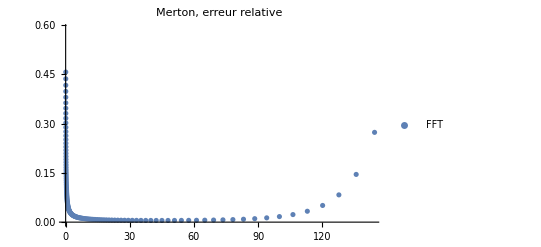

```mathematica
ListPlot[Xx,PlotLabel->"Merton, erreur relative", PlotLegends->{"FFT", "NIntegrate"},ImageSize->Full]
```

```mathematica
FFT={{0.052759,149.775843},{0.056098,147.658298},{0.059648,145.635632},{0.063422,143.703555},{0.067436,141.857969},{0.071703,140.094958},{0.076241,138.410779},{0.081065,136.801859},{0.086195,135.264782},{0.091650,133.796283},{0.097449,132.393243},{0.103616,131.052680},{0.110173,129.771745},{0.117145,128.547714},{0.124558,127.377983},{0.132440,126.260061},{0.140821,125.191569},{0.149732,124.170228},{0.159207,123.193860},{0.169282,122.260383},{0.179994,121.367803},{0.191384,120.514210},{0.203495,119.697779},{0.216373,118.916759},{0.230065,118.169477},{0.244624,117.454325},{0.260104,116.769766},{0.276563,116.114324},{0.294064,115.486583},{0.312673,114.885186},{0.332459,114.308827},{0.353497,113.756253},{0.375867,113.226260},{0.399652,112.717687},{0.424942,112.229420},{0.451833,111.760380},{0.480426,111.309532},{0.510827,110.875873},{0.543153,110.458434},{0.577524,110.056279},{0.614070,109.668498},{0.652929,109.294210},{0.694247,108.932559},{0.738179,108.582711},{0.784892,108.243852},{0.834561,107.915187},{0.887372,107.595940},{0.943526,107.285346},{1.003233,106.982656},{1.066718,106.687130},{1.134221,106.398038},{1.205996,106.114657},{1.282312,105.836268},{1.363458,105.562156},{1.449739,105.291607},{1.541479,105.023906},{1.639025,104.758336},{1.742744,104.494173},{1.853026,104.230687},{1.970287,103.967139},{2.094969,103.702777},{2.227540,103.436838},{2.368501,103.168539},{2.518381,102.897080},{2.677746,102.621640},{2.847196,102.341373},{3.027369,102.055407},{3.218944,101.762841},{3.422641,101.462739},{3.639228,101.154131},{3.869522,100.836006},{4.114388,100.507313},{4.374750,100.166952},{4.651588,99.813775},{4.945944,99.446578},{5.258927,99.064100},{5.591716,98.665014},{5.945565,98.247930},{6.321805,97.811381},{6.721854,97.353824},{7.147218,96.873633},{7.599500,96.369090},{8.080403,95.838384},{8.591737,95.279598},{9.135429,94.690710},{9.713526,94.069577},{10.328206,93.413933},{10.981783,92.721379},{11.676720,91.989372},{12.415632,91.215220},{13.201303,90.396069},{14.036692,89.528889},{14.924946,88.610473},{15.869408,87.637412},{16.873637,86.606093},{17.941415,85.512681},{19.076762,84.353103},{20.283955,83.123037},{21.567540,81.817891},{22.932351,80.432790},{24.383529,78.962557},{25.926538,77.401690},{27.567191,75.744347},{29.311665,73.984319},{31.166531,72.115009},{33.138774,70.129407},{35.235823,68.020066},{37.465574,65.779068},{39.836426,63.398001},{42.357307,60.867930},{45.037712,58.179373},{47.887735,55.322313},{50.918109,52.286294},{54.140248,49.060757},{57.566287,45.635908},{61.209128,42.004655},{65.082492,38.166312},{69.200964,34.132697},{73.580057,29.936507},{78.236263,25.640318},{83.187117,21.342571},{88.451265,17.175700},{94.048533,13.292713},{100.000000,9.842642},{106.328081,6.941029},{113.056608,4.645595},{120.210922,2.946483},{127.817966,1.774595},{135.906390,1.023838},{144.506657,0.577914},{153.651155,0.332333},{163.374325,0.206464},{173.712784,0.145707},{184.705470,0.117239},{196.393781,0.103413},{208.821739,0.095704},{222.036148,0.090398},{236.086775,0.086033},{251.026537,0.082081}};
```